```mathematica
S=NDSolve[{u''[t]==2*(v[t]-u[t])/Norm[v[t]-u[t]]^3, v''[t]== 2*(u[t]-v[t])/Norm[v[t]-u[t]]^3, u[0]=={0,0.5}, v[0]=={0,-0.5}, u'[0]=={0.7,0}, v'[0]=={-0.7,0}}, {u,v}, {t,0,40}]
```

{{u→InterpolatingFunction[{{0., 40.}}, <>],v→InterpolatingFunction[{{0., 40.}}, <>]}}

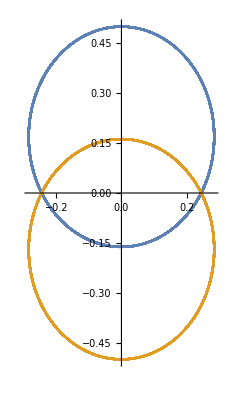

Clear::ssym: u'[0] is not a symbol or a string.

Clear::ssym: v'[0] is not a symbol or a string.

```mathematica
ParametricPlot[{Evaluate[u[t] /. S],Evaluate[v[t] /.S]}, {t,0,40}]
```